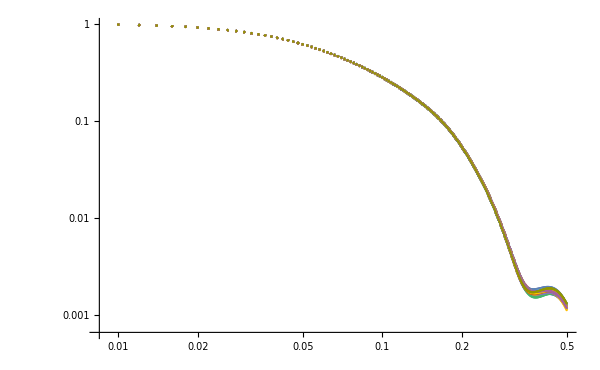

```mathematica
lsf[n_]:=Import["SAS_alpha-curve_tot_10%_r=6_seed_"<>ToString[n]<>".dat"];
ListLogLogPlot[Table[lsf[i],{i,1,100}],PlotRange->All,ImageSize->600]
```

```mathematica
listableinterpolsf=Table[Interpolation[lsf[i]],{i,1,100}];
```

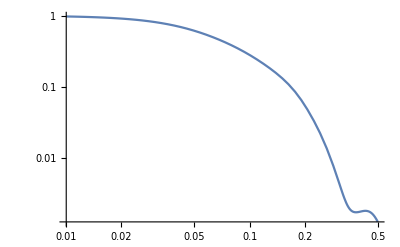

```mathematica
avgsf[x_]:=Sum[listableinterpolsf⟦i⟧[x],{i,1,100}]/100;
avgplotsf=LogLogPlot[avgsf[x],{x,Max[Table[Min[lsf[i]⟦All,1⟧],{i,1,100}]],Min[Table[Max[lsf[i]⟦All,1⟧],{i,1,100}]]},PlotRange->All]
```

```mathematica
avgsfdata=Table[{x,avgsf[x]},{x,Max[Table[Min[lsf[i]⟦All,1⟧],{i,1,100}]],Min[Table[Max[lsf[i]⟦All,1⟧],{i,1,100}]],.002}];
```

```mathematica
Export["mean_SAS.dat",avgsfdata]
```

mean_100_SAS_alpha-curve_100%_rmax=6.dat

```mathematica
(*calculating standard errors of the mean*)
```

```mathematica
readysf=Table[listableinterpolsf⟦i⟧[j],{i,1,100},{j,Max[Table[Min[lsf[k]⟦All,1⟧],{k,1,100}]],Min[Table[Max[lsf[k]⟦All,1⟧],{k,1,100}]],.002}];
```

```mathematica
Length[avgsfdata]
```

496

```mathematica
SEMSF=Table[StandardDeviation[readysf⟦All,i⟧]/Sqrt[Length[readysf⟦All,i⟧]],{i,1,146}];
Length[SEMSF]
```

146

```mathematica
qSEMSF=Table[i,{i,0.01,.3,.002}];
Length[qSEMSF]
```

146

```mathematica
SEMSFdata=Table[{qSEMSF⟦i⟧,SEMSF⟦i⟧},{i,1,Length[qSEMSF]}];
Export["SEM-SAS.dat",SEMSFdata]
```

SEM-SAS_alpha-curves_100%_rmax=6.dat